```mathematica
450777
```

450777

```mathematica
450777 24
```

10818648

```mathematica
829.50-340.50
```

489.

```mathematica
(a-b)/c
```

(a-b)/c

```mathematica
(1000-9999)/□
```

```mathematica
(a-b)/a
```

(a-b)/a

```mathematica
Simplify[(a-b)/a]
```

1-b/a

```mathematica
Plot3D[1-b/a,{a,-8,8},{b,-8,8}]
```

-Graphics3D-

```mathematica
Plot3D[1-b/a,{a,-8,8},{b,-8,8}, AxesLabel->{a,b}]
```

-Graphics3D-

```mathematica
Plot3D[1-b/a,{a,0,10},{b,0,10}, AxesLabel->{a,b}]
```

-Graphics3D-

```mathematica
Plot3D[1-b/a,{a,0,100},{b,0,100}, AxesLabel->{a,b}]
```

-Graphics3D-

```mathematica
With[{a=1000, b=9999},
(a-b)/a]
```

-8999/1000

```mathematica
With[{a=1000, b=999},
(a-b)/a]
```

1/1000

```mathematica
With[{a=1000, b=999},
Abs[a-b]/a]
```

1/1000

```mathematica
N[1/1000]
```

0.001

```mathematica
With[{a=1100, b=999},
Abs[a-b]/a]
```

101/1100

```mathematica
N[101/1100]
```

0.0918182

```mathematica
With[{a=2100, b=999},
Abs[a-b]/a]
```

367/700

```mathematica
N[367/700]
```

0.524286

```mathematica
D[u[x,t],t]==D[u[x,t],{x,2}]
```

u^(0,1)[x,t]==u^(2,0)[x,t]

```mathematica
DSolve[Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],{u[x,t],u[x,t]},{t,x}]
```

DSolve[u^(0,1)[x,t]==u^(2,0)[x,t],{u[x,t],u[x,t]},{t,x}]

```mathematica
heqn=D[u[x,t],t]==D[u[x,t],{x,2}];
```

```mathematica
ic=u[x,0]==E^(-x^2);
```

```mathematica
sol=DSolveValue[{heqn,ic},u[x,t],{x,t}]
```

(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t))

```mathematica
Plot3D[sol,{t,-2.7074787643449203,2.7074787643449203},{x,-1.411408476546777,1.411408476546777}]
```

General::munfl: Exp[-1452.37] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1167.46] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1059.51] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
DSolveValue[
{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==E^(-x^2)},
u[x,t],{x,t}]
```

(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t))

```mathematica
DSolveValue[
{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==f[x]},
u[x,t],{x,t}]
```

Integrate[(ⅇ^(-(x-K[1])^2/(4 t)) f[K[1]])/(2 √π √t),{K[1],-∞,∞},Assumptions→t>0]

```mathematica
DSolveValue[
{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==x},
u[x,t],{x,t}]
```

x

```mathematica
DSolveValue[
{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==x^2},
u[x,t],{x,t}]
```

2 t+x^2

```mathematica
Plot3D[2 t+x^2,{t,-3.,3.},{x,-2.2882456112707374,2.2882456112707374}]
```

-Graphics3D-

```mathematica
Plot3D[2 t+x^2,{t,0,3.},{x,-2.2882456112707374,2.2882456112707374}]
```

-Graphics3D-

```mathematica
Plot3D[2 t+x^2,{t,0,3.},{x,-2.2882456112707374,2.2882456112707374}, AxesLabel->{t,x}]
```

-Graphics3D-

```mathematica
DSolveValue[
{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Sin[x]},
u[x,t],{x,t}]
```

ⅇ^-t Sin[x]

```mathematica
Plot3D[ⅇ^-t Sin[x],{t,-3.843819601921041,3.843819601921041},{x,-6.283185307179586,6.283185307179586}]
```

-Graphics3D-

```mathematica
Plot3D[ⅇ^-t Sin[x],{t,0,2π},{x,-2π,2π}]
```

-Graphics3D-

```mathematica
Plot3D[ⅇ^-t Sin[x],{t,0,2π},{x,-2π,2π}, AxesLabel->{t, x}]
```

-Graphics3D-

```mathematica
D[U[x,t],2]
```

General::ivar: 2 is not a valid variable.

∂_2 U[x,t]

```mathematica
D[U[x,t],{t,2}]
```

U^(0,2)[x,t]

```mathematica
D[U[x,t],{x,2}]
```

U^(2,0)[x,t]

```mathematica
D[U[x,t],t]==α D[U[x,t],{x,2}]
```

U^(0,1)[x,t]==α U^(2,0)[x,t]

```mathematica
DSolve[Derivative[0,1][U][x,t]==α Derivative[2,0][U][x,t],{U[x,t],U[x,t]},{t,x}]
```

DSolve[U^(0,1)[x,t]==α U^(2,0)[x,t],{U[x,t],U[x,t]},{t,x}]

```mathematica
D[U[x,t], x]
```

U^(1,0)[x,t]

```mathematica
ComplexPlot3D[Gamma[z],{z,-4-4I,4+4I}]
```

ComplexPlot3D[Gamma[z],{z,-4-4 ⅈ,4+4 ⅈ}]

```mathematica
∫Sqrt[Sqrt[x]+Sqrt[2 x+2 Sqrt[x]+1]+1] ⅆx
```

∫√(1+√x+√(1+2 √x+2 x))ⅆx

```mathematica
FullSimplify[∫√(1+√x+√(1+2 √x+2 x))ⅆx]
```

∫√(1+√x+√(1+2 (√x+x)))ⅆx

```mathematica
∫x^2/(ProductLog[a/x]+1) ⅆx
```

∫x^2/(1+ProductLog[a/x])ⅆx

```mathematica
∫_a^b f[x]ⅆx
```

∫_a^b f[x]ⅆx

```mathematica
∫_a^b xⅆx
```

-a^2/2+b^2/2

```mathematica
Simplify[-a^2/2+b^2/2]
```

1/2 (-a^2+b^2)

```mathematica
Plot3D[1/2 (-a^2+b^2),{a,-5.99070478491457,5.99070478491457},{b,-5.99070478491457,5.99070478491457}]
```

-Graphics3D-

```mathematica
∫_a^b Sin[x]ⅆx
```

Cos[a]-Cos[b]

```mathematica
Plot3D[Cos[a]-Cos[b],{a,-3.903133887390964,3.903094878648954},{b,-3.9030982863212005,3.903130303543679}]
```

-Graphics3D-

```mathematica
Plot3D[Cos[a]-Cos[b],Element[{a,b}, Disk[]]]
```

-Graphics3D-

```mathematica
Plot3D[Cos[a]-Cos[b],Element[{a,b}, Disk[{0,0}, 10]]]
```

-Graphics3D-

```mathematica
True
```

True

```mathematica
True[]
```

True[]

```mathematica
FullForm[True[]]
```

True[]

```mathematica
True[][[0]]
```

True

```mathematica
True[][[1]]
```

Part::partw: Part 1 of True[] does not exist.

True[]⟦1⟧

```mathematica
List[True]
```

{True}




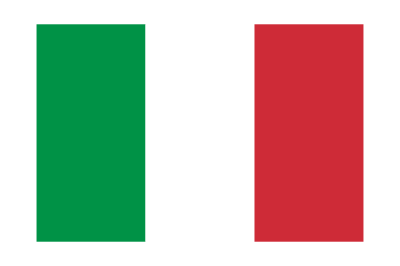
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[EntityClass["Country", {EntityProperty["Country", "EntityClasses"] -> EntityClass["Country", "Europe"], EntityProperty["Country", "Population"] -> TakeLargest[5]}], EntityProperty["Country", "Flag"]]
```

```mathematica
EntityValue[EntityClass["Country", {EntityProperty["Country", "EntityClasses"] -> EntityClass["Country", "Europe"], EntityProperty["Country", "Population"] -> TakeLargest[5]}], EntityProperty["Country", "Flag"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
LinguisticAssistant
```

```mathematica
DSolveValue[
{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==x Sin[x]},
u[x,t],{x,t}]
```

$Aborted

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==x^3},u[x,t], {x,t}]
```

{{u[x,t]→6 t x+x^3}}

```mathematica
DSolveValue[
{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==x^3},
u[x,t],{x,t}]
```

6 t x+x^3

```mathematica
Plot3D[6 t x+x^3,{t,-0.8611111111111112,0.8611111111111112},{x,-0.8611111111111112,0.8611111111111112}]
```

-Graphics3D-

```mathematica
Plot3D[6 t x+x^3,{t,0,0.8611111111111112},{x,-1,1}, AxesLabel->{t,x}]
```

-Graphics3D-

```mathematica
DSolveValue[
{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Exp[x^2]},
u[x,t],{x,t}]
```

$Aborted

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Exp[x^2]},u[x,t], {x,t}]
```

$Aborted

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Exp[x]},u[x,t], {x,t}]
```

{{u[x,t]→ⅇ^(t+x)}}

```mathematica
{{u[x,t]->ⅇ^(t+x)}}⟦1,1,2⟧
```

ⅇ^(t+x)

```mathematica
Plot3D[ⅇ^(t+x),{t,-5.895879734614027,5.895879734614027},{x,-5.895879734614027,5.895879734614027}]
```

-Graphics3D-

```mathematica
Plot3D[ⅇ^(t+x),{t,0,5.895879734614027},{x,-5.895879734614027,5.895879734614027}]
```

-Graphics3D-

```mathematica
LinguisticAssistant
```

```mathematica
Information[a]
```

Global`a

```mathematica
Information[D]
```

D[f,x] gives the partial derivative ∂f/∂x. 
D[f,{x,n}] gives the multiple derivative ∂^n f/∂x^n.
D[f,x,y,…] gives the partial derivative ⋯ (∂/∂y)(∂/∂x) f.
D[f,{x,n},{y,m},…] gives the multiple partial derivative ⋯ (∂^m /∂y^m)(∂^n /∂x^n) f.
D[f,{{x_1,x_2,…}}] for a scalar f gives the vector derivative (∂f/∂x_1,∂f/∂x_2,…). 
D[f,{array}] gives an array derivative.

Attributes[D]={Protected,ReadProtected}
 
Options[D]:={NonConstants→{}}

```mathematica
Information[Integer]
```

Integer is the head used for integers.

Attributes[Integer]={Protected}

```mathematica
Integer[3]
```

Integer[3]

```mathematica
Information[DSolve]
```

DSolve[eqn,u,x] solves a differential equation for the function u, with independent variable x. 
DSolve[eqn,u,{x,x_min,x_max}] solves a differential equation for x between x_min and x_max.
DSolve[{eqn_1,eqn_2,…},{u_1,u_2,…},…] solves a list of differential equations. 
DSolve[eqn,u,{x_1,x_2,…}] solves a partial differential equation. 
DSolve[eqn,u,{x_1,x_2,…}∈Ω] solves the partial differential equation eqn over the region Ω.

Attributes[DSolve]={Protected,ReadProtected}
 
Options[DSolve]:={Assumptions:>$Assumptions,DiscreteVariables→{},GeneratedParameters→C,Method→Automatic}

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Exp[-x^2]},u[x,t], {x,t}]
```

{{u[x,t]→(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t))}}

```mathematica
{{u[x,t]->(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t))}}⟦1,1,2⟧
```

(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t))

```mathematica
Plot3D[(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t)),{t,-2.7074787643449203,2.7074787643449203},{x,-1.411408476546777,1.411408476546777}]
```

General::munfl: Exp[-1452.37] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1167.46] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1059.51] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t)),{t,0,2.7074787643449203},{x,-1.411408476546777,1.411408476546777}]
```

-Graphics3D-

```mathematica
Plot3D[(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t)),{t,0,2.7074787643449203},{x,-1.411408476546777,1.411408476546777}, AxesLabel->{t, x}]
```

-Graphics3D-

```mathematica
Plot3D[(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t)),{t,0,10},{x,-10,10}, AxesLabel->{t, x}]
```

-Graphics3D-

```mathematica
Plot3D[(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t)),{t,0,50},{x,-10,10}, AxesLabel->{t, x}]
```

-Graphics3D-

```mathematica
Plot3D[(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t)),{t,0,50},{x,-10,10}, AxesLabel->{t, x}]
```

```mathematica
Plot3D[(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t)),{t,0,100},{x,-10,10}, AxesLabel->{t, x}]
```

-Graphics3D-

```mathematica
Plot3D[(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t)),{t,0,100},{x,-10,10},Mesh->Automatic,MeshFunctions->{#3&},AxesLabel->{t,x}]
```

-Graphics3D-

```mathematica
Plot3D[(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t)),{t,0,100},{x,-10,10},PlotStyle->Directive[RGBColor[0.9400000000000001,0.,0.24],Opacity[0.652]],Mesh->Automatic,MeshFunctions->{#3&},AxesLabel->{t,x}]
```

-Graphics3D-

```mathematica
Plot3D[(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t)),{t,0,1000},{x,-10,10},PlotStyle->Directive[RGBColor[0.9400000000000001,0.,0.24],Opacity[0.652]],Mesh->Automatic,MeshFunctions->{#3&},AxesLabel->{t,x}]
```

-Graphics3D-

```mathematica
DSolveValue[
{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==x},
u[x,t],{x,t}]
```

x

```mathematica
DSolveValue[
{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==2x},
u[x,t],{x,t}]
```

2 x

```mathematica
DSolveValue[
{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Exp[x]},
u[x,t],{x,t}]
```

ⅇ^(t+x)

```mathematica
DSolveValue[
{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Exp[x]^2},
u[x,t],{x,t}]
```

ⅇ^(4 t+2 x)

```mathematica
DSolveValue[
{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Exp[x^2]},
u[x,t],{x,t}]
```

$Aborted

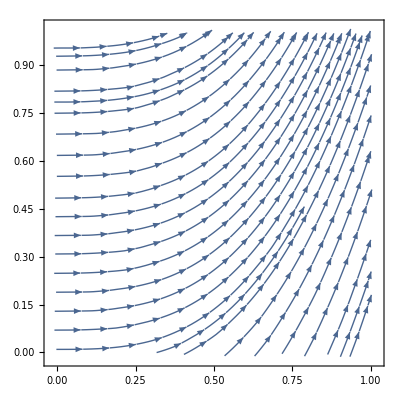

```mathematica
StreamPlot[
{1, 3 x^2}, {x,y}∈Rectangle[], ColorFunction->"Rainbow"]
```

```mathematica
StreamPlot[
{1, 3 x^2}, {x,y}∈Square[3], ColorFunction->"Rainbow"]
```

StreamPlot::idomdim: {x,y}∈□3 does not have a valid dimension as a plotting domain.

StreamPlot[{1,3 x^2},{x,y}∈□3,ColorFunction→Rainbow]

```mathematica
StreamPlot[
{1, 3 x^2}, {x,y}∈Rectangle[3], ColorFunction->"Rainbow"]
```

StreamPlot::idomdim: {x,y}∈Rectangle[3] does not have a valid dimension as a plotting domain.

StreamPlot[{1,3 x^2},{x,y}∈Rectangle[3],ColorFunction→Rainbow]

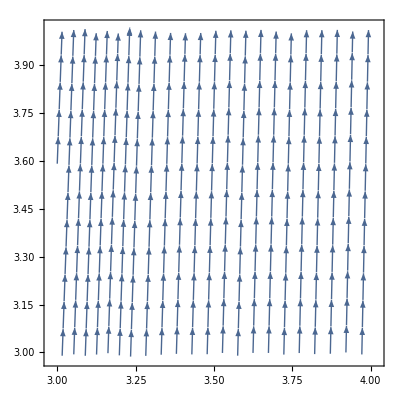

```mathematica
StreamPlot[
{1, 3 x^2}, {x,y}∈Rectangle[{3,3}], ColorFunction->"Rainbow"]
```

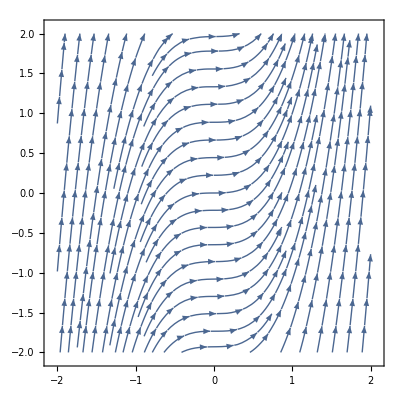

```mathematica
StreamPlot[
{1, 3 x^2}, {x, -2, 2}, {y, -2, 2}, ColorFunction->"Rainbow"]
```

```mathematica
StreamPlot[
{1, 3 x^2}, {x, -2, 2}, {y, -2, 2}, ColorFunction->"Rainbow"]
```

-Graphics-

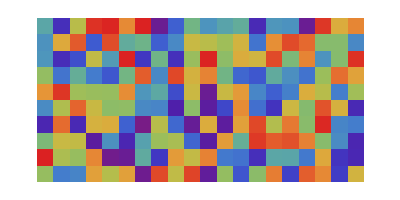

```mathematica
ArrayPlot[RandomReal[1,{10,20}],ColorFunction->"Rainbow"]
```

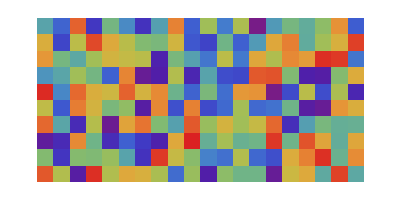

```mathematica
ArrayPlot[RandomReal[1,{10,20}],ColorFunction->"Rainbow"]
```

```mathematica
StreamPlot[
{1, 3 x^2}, {x, -2, 2}, {y, -2, 2}, ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
StreamPlot[
{1, 3 x^2}, {x, -2, 2}, {y, -2, 2}]
```

-Graphics-

```mathematica
Image3D[ExampleData[{"TestImage3D","CTengine"}],ColorFunction->"RainbowOpacity"]
```

-Graphics3D-

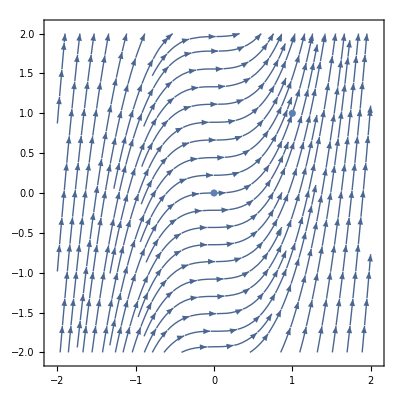

```mathematica
Show[{
StreamPlot[
{1, 3 x^2}, {x, -2, 2}, {y, -2, 2}],
ListPlot[{{0, 0}, {1,1}}]}]
```

```mathematica
Show[{
StreamPlot[
{1, 3 x^2}, {x, -2, 2}, {y, -2, 2}],
ListPlot[{{0, 0}, {1,1}}]}]
```

```mathematica
{x[t]==1, y[t]==3 x[t]^2,x[0]==0, y[0]==0,x[1]==1,y[1]==1}
```

{x[t]==1,y[t]==3 x[t]^2,x[0]==0,y[0]==0,x[1]==1,y[1]==1}

```mathematica
DSolve[{x[t]==1, y[t]==3 x[t]^2,x[0]==0, y[0]==0,x[1]==1,y[1]==1}, {x[t], y[t]}, t]
```

DSolve[{x[t]==1,y[t]==3 x[t]^2,x[0]==0,y[0]==0,x[1]==1,y[1]==1},{x[t],y[t]},t]

```mathematica
DSolveValue[{x[t]==1, y[t]==3 x[t]^2,x[0]==0, y[0]==0,x[1]==1,y[1]==1}, {x[t], y[t]}, t]
```

DSolveValue[{x[t]==1,y[t]==3 x[t]^2,x[0]==0,y[0]==0,x[1]==1,y[1]==1},{x[t],y[t]},t]

```mathematica
{x'[t]==1,y'[t]==3 x[t]^2,x[0]==0,y[0]==0,x[1]==1,y[1]==1}
```

{x'[t]==1,y'[t]==3 x[t]^2,x[0]==0,y[0]==0,x[1]==1,y[1]==1}

```mathematica
NDSolve[{x'[t]==1,y'[t]==3 x[t]^2,x[0]==0,y[0]==0,x[1]==1,y[1]==1},{x[t],y[t]},{t,0,2}]
```

NDSolve::ndnco: The number of constraints (4) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (2).

NDSolve[{x'[t]==1,y'[t]==3 x[t]^2,x[0]==0,y[0]==0,x[1]==1,y[1]==1},{x[t],y[t]},{t,0,2}]

```mathematica
DSolve[{x'[t]==1,y'[t]==3 x[t]^2,x[0]==0,y[0]==0,x[1]==1,y[1]==1},{x[t],y[t]},{t}]
```

{{x[t]→t,y[t]→t^3}}

```mathematica
DSolveValue[{x'[t]==1,y'[t]==3 x[t]^2,x[0]==0,y[0]==0,x[1]==1,y[1]==1},{x[t],y[t]},{t}]
```

{t,t^3}

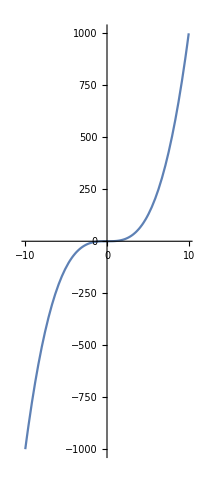

```mathematica
ParametricPlot[{t,t^3},{t,-10,10}]
```

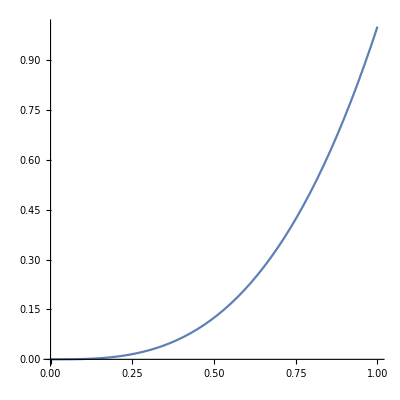

```mathematica
ParametricPlot[{t,t^3},{t,0,1}]
```

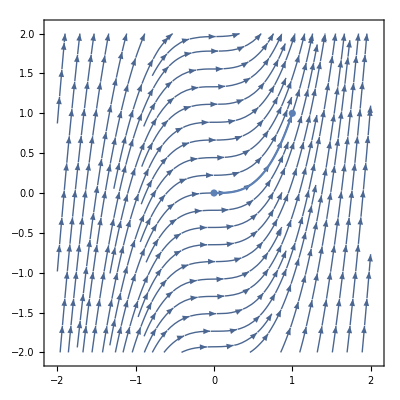

```mathematica
Show[{
StreamPlot[
{1, 3 x^2}, {x, -2, 2}, {y, -2, 2}],
ListPlot[{{0, 0}, {1,1}}],
ParametricPlot[{t,t^3},{t,0,1}]}]
```

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->Function[{x,y,z},Hue[z]]]
```

-Graphics3D-

```mathematica
D[U[x,t],t]==α D[U[x,t],{x,2}]
```

U^(0,1)[x,t]==α U^(2,0)[x,t]

```mathematica
DSolve[Derivative[0,1][U][x,t]==α Derivative[2,0][U][x,t],{U[x,t],U[x,t]},{t,x}]
```

DSolve[U^(0,1)[x,t]==α U^(2,0)[x,t],{U[x,t],U[x,t]},{t,x}]

```mathematica
DSolve[Derivative[0,1][U][x,t]==α Derivative[2,0][U][x,t],U[x,t],{t,x}]
```

DSolve[U^(0,1)[x,t]==α U^(2,0)[x,t],U[x,t],{t,x}]

```mathematica
DSolve[{Derivative[0,1][U][x,t]==α Derivative[2,0][U][x,t], U[x,0]==Sin[x]},U[x,t],{t,x}]
```

DSolve[{U^(0,1)[x,t]==α U^(2,0)[x,t],U[x,0]==Sin[x]},U[x,t],{t,x}]

```mathematica
DSolveValue[{Derivative[0,1][U][x,t]==α Derivative[2,0][U][x,t], U[x,0]==Sin[x]},U[x,t],{t,x}]
```

DSolveValue[{U^(0,1)[x,t]==α U^(2,0)[x,t],U[x,0]==Sin[x]},U[x,t],{t,x}]

```mathematica
DSolveValue[{Derivative[0,1][U][x,t]==Derivative[2,0][U][x,t], U[x,0]==Sin[x]},U[x,t],{t,x}]
```

DSolveValue[{U^(0,1)[x,t]==U^(2,0)[x,t],U[x,0]==Sin[x]},U[x,t],{t,x}]

```mathematica
FullSimplify[
1==Normalize[{1, 3 x^2}].
Normalize[{1-x, 1-f[x]}], Element[x|f[x],Reals]]
```

(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))==1

```mathematica
FindInstance[(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))==1,{x}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))==1,{x}]

```mathematica
Reduce[(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))==1]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))==1]

```mathematica
Reduce[(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))==1, f[x], Reals]
```

x<1&&f[x]==1-3 x^2+3 x^3

```mathematica
FindInstance[x<1&&f[x]==1-3 x^2+3 x^3,{x}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[x<1&&f[x]==1-3 x^2+3 x^3,{x}]

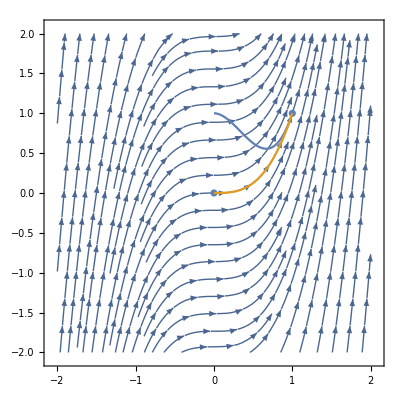

```mathematica
Show[{
StreamPlot[
{1, 3 x^2}, {x, -2, 2}, {y, -2, 2}],
ListPlot[{{0, 0}, {1,1}}],
Plot[{1-3 x^2+3 x^3,x^3},{x,0,1}]}]
```

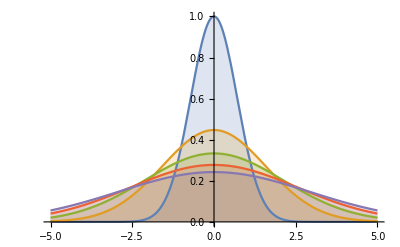

```mathematica
Plot[Evaluate[Table[sol,{t,0,4}]],{x,-5,5},PlotRange->All,Filling->Axis]
```

```mathematica
sol
```

(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t))

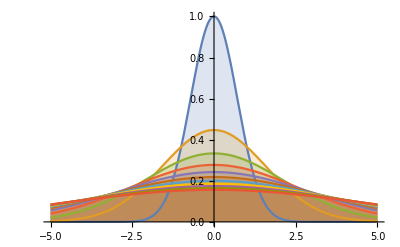

```mathematica
Plot[
Evaluate[
Table[(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t)),{t,0,10, 1}]],
{x,-5,5},
PlotRange->All,Filling->Axis]
```

```mathematica
DSolveValue[{x'[t]==1,y'[t]==3 x[t]^2,x[0]==0,y[0]==0,x[1]==1,y[1]==1},{x[t],y[t]},{t}]
```

```mathematica
DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==-x^2},u[x,t], {x,t}]
```

{{u[x,t]→-2 t-x^2}}

```mathematica
DSolveValue[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==-x^2},u[x,t], {x,t}]
```

-2 t-x^2

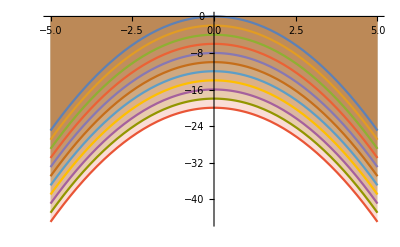

```mathematica
Plot[
Evaluate[
Table[-2 t-x^2,{t,0,10, 1}]],
{x,-5,5},
PlotRange->All,Filling->Axis]
```

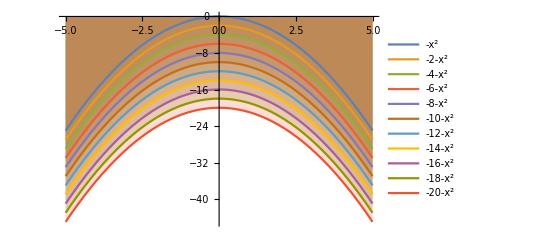

```mathematica
Plot[
Evaluate[
Table[-2 t-x^2,{t,0,10, 1}]],
{x,-5,5},
PlotRange->All,Filling->Axis, PlotLegends->"Expressions"]
```

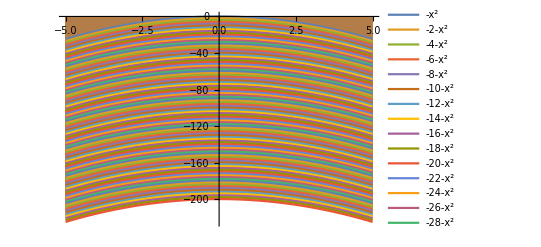

```mathematica
Plot[
Evaluate[
Table[-2 t-x^2,{t,0,100, 1}]],
{x,-5,5},
PlotRange->All,Filling->Axis, PlotLegends->"Expressions"]
```

```mathematica
DSolveValue[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==x^3},u[x,t], {x,t}]
```

6 t x+x^3

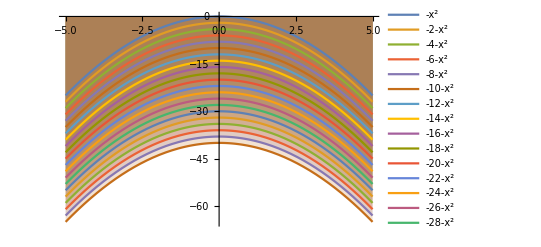

```mathematica
Plot[
Evaluate[
Table[-2 t-x^2,{t,0,20, 1}]],
{x,-5,5},
PlotRange->All,Filling->Axis, PlotLegends->"Expressions"]
```

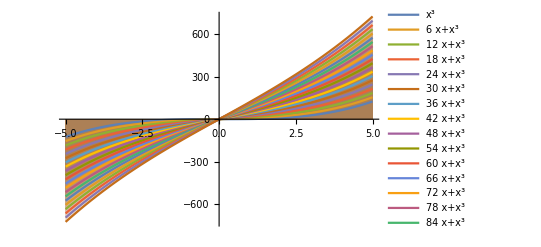

```mathematica
Plot[
Evaluate[
Table[6 t x+x^3,{t,0,20, 1}]],
{x,-5,5},
PlotRange->All,Filling->Axis, PlotLegends->"Expressions"]
```

```mathematica
Sin[x]/x
```

Sin[x]/x

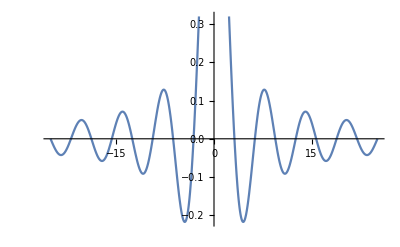

```mathematica
Plot[Sin[x]/x,{x,-25.132741228718345,25.132741228718345}]
```

```mathematica
DSolveValue[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Sin[x]/x},u[x,t], {x,t}]
```

$Aborted

```mathematica
DSolveValue[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Sin[x]},u[x,t], {x,t}]
```

ⅇ^-t Sin[x]

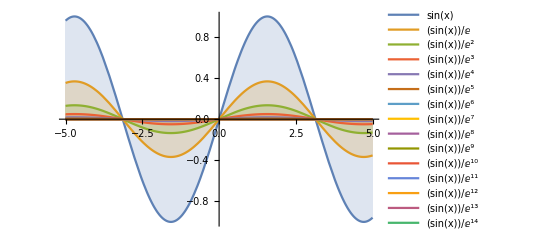

```mathematica
Plot[
Evaluate[
Table[ⅇ^-t Sin[x],{t,0,20, 1}]],
{x,-5,5},
PlotRange->All,Filling->Axis, PlotLegends->"Expressions"]
```

```mathematica
Exp[Sin[x]]
```

ⅇ^Sin[x]

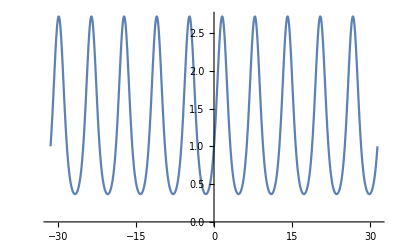

```mathematica
Plot[ⅇ^Sin[x],{x,-10 π,10 π}]
```

```mathematica
DSolveValue[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Exp[Sin[x]]},u[x,t], {x,t}]
```

$Aborted

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
DSolveValue[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==(ⅇ^(-x^2/2))/(√(2 π))},u[x,t], {x,t}]
```

(ⅇ^(-x^2/(2+4 t)))/(√(2 π) √(1+2 t))

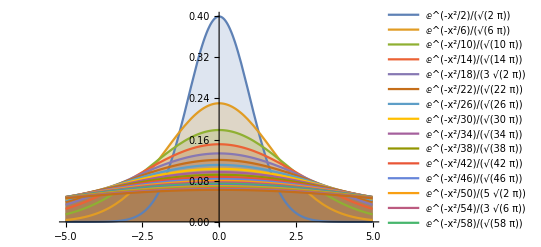

```mathematica
Plot[
Evaluate[
Table[(ⅇ^(-x^2/(2+4 t)))/(√(2 π) √(1+2 t)),{t,0,20, 1}]],
{x,-5,5},
PlotRange->All,Filling->Axis, PlotLegends->"Expressions"]
```

```mathematica
D[{1, 3 x^2},{x,2}]
```

{0,6}

```mathematica
D[{1, 3 x^2},{y,2}]
```

0

```mathematica
DSolveValue[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==√x},u[x,t], {x,t}]
```

(ⅇ^(-x^2/(8 t)) √π (√-x-ⅈ √x) (-x^2 BesselI[-1/4,x^2/(8 t)]+(4 t+x^2) BesselI[1/4,x^2/(8 t)]+x^2 (-BesselI[3/4,x^2/(8 t)]+BesselI[5/4,x^2/(8 t)])))/(8 √t Abs[x])

```mathematica
FullSimplify[(ⅇ^(-x^2/(8 t)) √π (√-x-ⅈ √x) (-x^2 BesselI[-1/4,x^2/(8 t)]+(4 t+x^2) BesselI[1/4,x^2/(8 t)]+x^2 (-BesselI[3/4,x^2/(8 t)]+BesselI[5/4,x^2/(8 t)])))/(8 √t Abs[x])]
```

(ⅇ^(-x^2/(8 t)) √π (√-x-ⅈ √x) (-x^2 BesselI[-1/4,x^2/(8 t)]+(4 t+x^2) BesselI[1/4,x^2/(8 t)]+x^2 (-BesselI[3/4,x^2/(8 t)]+BesselI[5/4,x^2/(8 t)])))/(8 √t Abs[x])

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

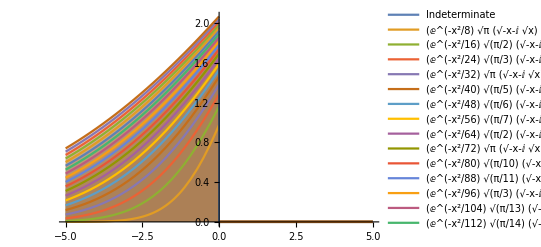

```mathematica
Plot[
Evaluate[
Table[(ⅇ^(-x^2/(8 t)) √π (√-x-ⅈ √x) (-x^2 BesselI[-1/4,x^2/(8 t)]+(4 t+x^2) BesselI[1/4,x^2/(8 t)]+x^2 (-BesselI[3/4,x^2/(8 t)]+BesselI[5/4,x^2/(8 t)])))/(8 √t Abs[x]),{t,0,20, 1}]],
{x,-5,5},
PlotRange->All,Filling->Axis, PlotLegends->"Expressions"]
```

```mathematica
DSolveValue[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Abs[x]},u[x,t], {x,t}]
```

1/2 ((4 ⅇ^(-x^2/(4 t)) √t)/(√π)+x+x Erf[x/(2 √t)]-x Erfc[x/(2 √t)])

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

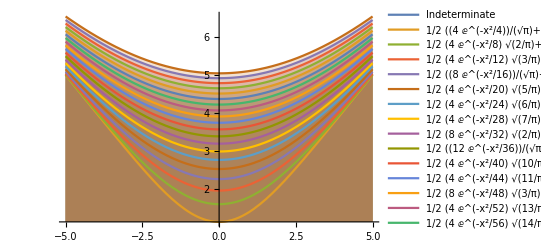

```mathematica
Plot[
Evaluate[
Table[1/2 ((4 ⅇ^(-x^2/(4 t)) √t)/(√π)+x+x Erf[x/(2 √t)]-x Erfc[x/(2 √t)]),{t,0,20, 1}]],
{x,-5,5},
PlotRange->All,Filling->Axis, PlotLegends->"Expressions"]
```

```mathematica
DSolveValue[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Identity[x]},u[x,t], {x,t}]
```

x

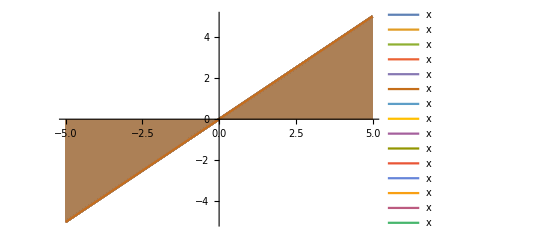

```mathematica
Plot[
Evaluate[
Table[
x,
{t,0,20, 1}]],
{x,-5,5},
PlotRange->All,Filling->Axis, PlotLegends->"Expressions"]
```

```mathematica
DSolveValue[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Sin[1/x]},u[x,t], {x,t}]
```

$Aborted

```mathematica
DSolveValue[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==1/x},u[x,t], {x,t}]
```

Integrate[(ⅇ^(-(x-K[1])^2/(4 t)))/(2 √π √t K[1]),{K[1],-∞,∞},Assumptions→t>0]

```mathematica
Integrate[(ⅇ^(-(x-K[1])^2/(4 t)))/(2 √π √t K[1]),{K[1],-∞,∞},Assumptions->t>0]/.t->1
```

Integrate::idiv: Integral of (ⅇ^(-(x-K[1])^2/(4 t)))/(2 √π √t K[1]) does not converge on {-∞,∞}.

Integrate::idiv: Integral of (ⅇ^(-1/4 (x-K[1])^2))/(2 √π K[1]) does not converge on {-∞,∞}.

Integrate[(ⅇ^(-1/4 (x-K[1])^2))/(2 √π K[1]),{K[1],-∞,∞},Assumptions→True]

```mathematica
DSolveValue[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==Log[x]},u[x,t], {x,t}]
```

1/2 (-EulerGamma+ⅈ π Erfc[x/(2 √t)]+Log[t]-Hypergeometric1F1^(1,0,0)[0,1/2,-x^2/(4 t)])

```mathematica
Plot[
Evaluate[
Table[
1/2 (-EulerGamma+ⅈ π Erfc[x/(2 √t)]+Log[t]-Derivative[1,0,0][Hypergeometric1F1][0,1/2,-x^2/(4 t)]),
{t,0,20, 1}]],
{x,-5,5},
PlotRange->All,Filling->Axis, PlotLegends->"Expressions"]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics-

```mathematica
-f[x]==f''[x]
```

-f[x]==f''[x]

```mathematica
DSolve[-f[x]==f''[x],{f[x]},{x}]
```

{{f[x]→C[1] Cos[x]+C[2] Sin[x]}}

```mathematica
{{f[x]->C[1] Cos[x]+C[2] Sin[x]}}⟦1,1,2⟧
```

C[1] Cos[x]+C[2] Sin[x]

```mathematica
TrigToExp[C[1] Cos[x]+C[2] Sin[x]]
```

1/2 ⅇ^(-ⅈ x) C[1]+1/2 ⅇ^(ⅈ x) C[1]+1/2 ⅈ ⅇ^(-ⅈ x) C[2]-1/2 ⅈ ⅇ^(ⅈ x) C[2]

```mathematica
Cos[x]+Sin[x]
```

Cos[x]+Sin[x]

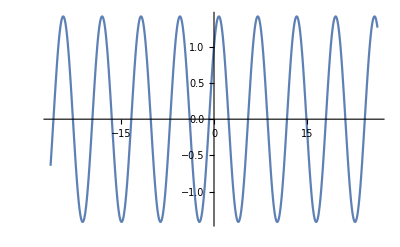

```mathematica
Plot[Cos[x]+Sin[x],{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
f'[x]==-f''[x]
```

f'[x]==-f''[x]

```mathematica
DSolve[f'[x]==-f''[x],{f[x],f[x]},{x}]
```

{{f[x]→-ⅇ^-x C[1]+C[2]}}

```mathematica
D[f[x],x]
```

f'[x]

```mathematica
f'[x]==λ f[x]
```

f'[x]==λ f[x]

```mathematica
DSolve[f'[x]==λ f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x λ) C[1]}}

```mathematica
D[f[x],x]==λ f[x]
```

f'[x]==λ f[x]

```mathematica
DSolve[f'[x]==λ f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x λ) C[1]}}

```mathematica
f[x]==x
```

f[x]==x

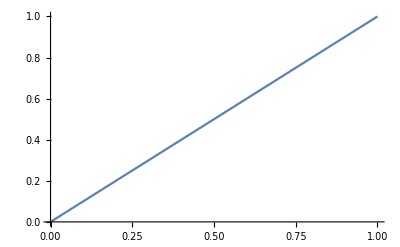

```mathematica
Plot[x, {x, 0, 1}]
```

```mathematica
Identity[f[x]]==λ f[x]
```

f[x]==λ f[x]

```mathematica
Reduce[f[x]==λ f[x]]
```

λ==1||f[x]==0

```mathematica
Laplacian[u[x,y],{x,y}]==0
```

u^(0,2)[x,y]+u^(2,0)[x,y]==0

```mathematica
DSolve[Derivative[0,2][u][x,y]+Derivative[2,0][u][x,y]==0,{u[x,y],u[x,y]},{x,y}]
```

{{u[x,y]→C[1][ⅈ x+y]+C[2][-ⅈ x+y]}}

```mathematica
Laplacian[u[x,y],{x,y}]
```

u^(0,2)[x,y]+u^(2,0)[x,y]

```mathematica
Laplacian[f[x],{x}]
```

f''[x]

```mathematica
Laplacian[f[x,y],{x}]
```

f^(2,0)[x,y]

```mathematica
Laplacian[f[x,y],{x, y}]
```

f^(0,2)[x,y]+f^(2,0)[x,y]

```mathematica
Laplacian[f[x,y,z],{x, y,z}]
```

f^(0,0,2)[x,y,z]+f^(0,2,0)[x,y,z]+f^(2,0,0)[x,y,z]

```mathematica
Ω=Rectangle[{0,0},{1,2}];
```

```mathematica
leqn=Laplacian[u[x,y],{x,y}]==0;
```

```mathematica
dcond=DirichletCondition[u[x,y]==Piecewise[{{UnitTriangle[2 x-1],y==0||y==2}},0],True];
```

```mathematica
sol=DSolveValue[{leqn,dcond},u[x,y],{x,y}∈Ω]//FullSimplify
```

(8 Cosh[π (-1+y) K[1]] Sech[π K[1]] Sin[1/2 π K[1]] Sin[π x K[1]])/(π^2 K[1]^2)K[1]1∞

```mathematica
Laplacian[f[x],x]
```

f[x]x

```mathematica
Laplacian[f[x],{x}]
```

f''[x]

```mathematica
Laplacian[f[x],{x}]==λ f[x]
```

f''[x]==λ f[x]

```mathematica
DSolve[f''[x]==λ f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x √λ) C[1]+ⅇ^(-x √λ) C[2]}}

```mathematica
-Laplacian[f[x],{x}]==λ f[x]
```

-f''[x]==λ f[x]

```mathematica
DSolve[-f''[x]==λ f[x],{f[x]},{x}]
```

{{f[x]→C[1] Cos[x √λ]+C[2] Sin[x √λ]}}

```mathematica
eqn=D[u[t,x],{t,2}]==D[u[t,x],{x,2}]+NeumannValue[-Derivative[1,0][u][t,x],x==0||x==1];
```

```mathematica
f[x_]=D[0.125 Erf[(x-0.5)/0.125],x];
vInit[x_]=-D[f[x],x];
ic={u[0,x]==f[x],Derivative[1,0][u][0,x]==vInit[x]};
```

```mathematica
bc=PeriodicBoundaryCondition[u[t,x],x==0,TranslationTransform[{1}]];
```

```mathematica
ufun=NDSolveValue[{eqn,ic,bc},u,{t,0,2},{x,0,1},Method->{"MethodOfLines"}];
```

```mathematica
plots=Table[Plot[ufun[t,x],{x,0,1},PlotRange->{-0.1,1.3}],{t,0,2,.1}];
ListAnimate[plots]
```

```mathematica
D[T[x,y,z,t], t]==α Laplacian[T[x,y,z], {x,y,z}]
```

T^(0,0,0,1)[x,y,z,t]==α (T^(0,0,2)[x,y,z]+T^(0,2,0)[x,y,z]+T^(2,0,0)[x,y,z])

```mathematica
DSolve[Derivative[0,0,0,1][T][x,y,z,t]==α (Derivative[0,0,2][T][x,y,z]+Derivative[0,2,0][T][x,y,z]+Derivative[2,0,0][T][x,y,z]),{T[x,y,z],T[x,y,z],T[x,y,z],T[x,y,z,t]},{t,x,y,z}]
```

DSolve::alliv: The function T[x,y,z] was specified without dependence on all the independent variables. Each function must depend on all the independent variables.

DSolve[T^(0,0,0,1)[x,y,z,t]==α (T^(0,0,2)[x,y,z]+T^(0,2,0)[x,y,z]+T^(2,0,0)[x,y,z]),{T[x,y,z],T[x,y,z],T[x,y,z],T[x,y,z,t]},{t,x,y,z}]

```mathematica
DSolve[Derivative[0,0,0,1][T][x,y,z,t]==(Derivative[0,0,2][T][x,y,z]+Derivative[0,2,0][T][x,y,z]+Derivative[2,0,0][T][x,y,z]),{T[x,y,z],T[x,y,z],T[x,y,z],T[x,y,z,t]},{t,x,y,z}]
```

DSolve::alliv: The function T[x,y,z] was specified without dependence on all the independent variables. Each function must depend on all the independent variables.

DSolve[T^(0,0,0,1)[x,y,z,t]==T^(0,0,2)[x,y,z]+T^(0,2,0)[x,y,z]+T^(2,0,0)[x,y,z],{T[x,y,z],T[x,y,z],T[x,y,z],T[x,y,z,t]},{t,x,y,z}]

```mathematica
D[T[x,y,z,t], t]==α Laplacian[T[x,y,z,t], {x,y,z}]
```

T^(0,0,0,1)[x,y,z,t]==α (T^(0,0,2,0)[x,y,z,t]+T^(0,2,0,0)[x,y,z,t]+T^(2,0,0,0)[x,y,z,t])

```mathematica
DSolve[Derivative[0,0,0,1][T][x,y,z,t]==α (Derivative[0,0,2,0][T][x,y,z,t]+Derivative[0,2,0,0][T][x,y,z,t]+Derivative[2,0,0,0][T][x,y,z,t]),{T[x,y,z,t],T[x,y,z,t],T[x,y,z,t],T[x,y,z,t]},{t,x,y,z}]
```

DSolve[T^(0,0,0,1)[x,y,z,t]==α (T^(0,0,2,0)[x,y,z,t]+T^(0,2,0,0)[x,y,z,t]+T^(2,0,0,0)[x,y,z,t]),{T[x,y,z,t],T[x,y,z,t],T[x,y,z,t],T[x,y,z,t]},{t,x,y,z}]

```mathematica
DSolve[Derivative[0,0,0,1][T][x,y,z,t]==(Derivative[0,0,2,0][T][x,y,z,t]+Derivative[0,2,0,0][T][x,y,z,t]+Derivative[2,0,0,0][T][x,y,z,t]),{T[x,y,z,t],T[x,y,z,t],T[x,y,z,t],T[x,y,z,t]},{t,x,y,z}]
```

DSolve[T^(0,0,0,1)[x,y,z,t]==T^(0,0,2,0)[x,y,z,t]+T^(0,2,0,0)[x,y,z,t]+T^(2,0,0,0)[x,y,z,t],{T[x,y,z,t],T[x,y,z,t],T[x,y,z,t],T[x,y,z,t]},{t,x,y,z}]

```mathematica
Entity["Chemical","Caffeine"]
```

```mathematica
Range[1]*10
```

{10}

```mathematica
LinguisticAssistant
```

```mathematica
FinancialData["
```

```mathematica
LinguisticAssistant
```

```mathematica
FinancialData["XAU/USD"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

$Failed